## Oscillations and Waves Exam 2

## April 4, 2025 Longitudinal Waves in Two Dimensions

## The Physics Problem: We are going to set off an explosion in the middle of a two-dimensional grid of masses. This will create a radially outward set of initial velocities, which will turn into radially outward displacements. The wave will also travel radially outward. Because we have radial displacement and radial wave motion, this notebook complements the previous notebook by illustrating longitudinal waves, also called “compression” waves. For multiple reasons, I am dropping back to two dimensions for this notebook (after we explored three dimensions in Tuesday’s notebook): (1) Three-dimensional simulations are taxing the heck out of some people’s laptops. (2) Three-dimensional simulations are harder to visualize simply due to the sheer crowding of the graphics. (3) It will be faster in an exam situation to only have to deal with code in two dimensions. (4) Most of the intuition you can build in three dimensions can be built in two or even one dimension. This is especially true of compression waves.

## Directions: After downloading this notebook, rename it with your first name in the filename. E.g., Eli-Exam2.nb, Harper-Exam2.nb, Hexi-Exam2.nb, Jeremy-Exam2.nb, Rania-Exam2.nb, Tahm-Exam2.nb, or Walker-Exam2.nb. Then disconnect from the wifi and work the exam. Save your notebook early and often so that you don’t lose work in progress. When you are done, save your notebook one last time, re-join the wifi, and then email it to me.

### Initial Conditions for the Simulation

Set up the duration, steps, and deltaT:

```mathematica
tInitial = 0.0;
tFinal = 5.0;
steps = 1200;
deltaT = (tFinal - tInitial)/steps;
```

Set up the size of the grid (enough masses so that the grid is recognizably starting to form a continuum, but not so many that we tax our computers). During debugging of the code, we will keep the number of masses very small:

### Initial Velocities and Positions for the Simulation

```mathematica
nx=31;  (* I chose an odd number so that if j goes from 1 to 31, *)
(* it is obvious that the center in the j index is at j=16. *)
ny=21; (* Again, an odd number so the center will be an integer. *)
```

```mathematica
initialXArray=Table[0,nx,ny];
initialYArray = Table[0,nx,ny];
explosionCenterX=(nx+1)/2;
explosionCenterY=(ny+1)/2;
explosionMagnitude = 10;
explosionBreadth=5;
initialVxArray=Array[
explosionMagnitude(#1-explosionCenterX)/explosionBreadth^2 Exp[-((#1-explosionCenterX)^2+(#2-explosionCenterY)^2)/explosionBreadth^2]&,
{nx,ny}
];
initialVyArray=Array[
explosionMagnitude(#2-explosionCenterY)/explosionBreadth^2 Exp[-((#1-explosionCenterX)^2+(#2-explosionCenterY)^2)/explosionBreadth^2]&,
{nx,ny}
];
initialConditions={tInitial,initialXArray,initialVxArray,initialYArray,initialVyArray};
```

### Displaying the Initial Velocities

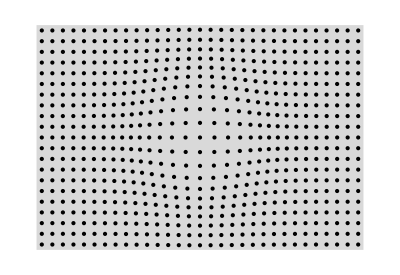

```mathematica
width=nx+1;
depth=ny+1;

xspacing=width/nx; 
yspacing=depth/ny; 
rectangle=Style[Rectangle[{-width/2,-depth/2},{width/2,depth/2}],LightGray];
pointRestPosition[j_,k_]:={-width/2+(j-1/2) xspacing,-depth/2+(k-1/2) yspacing}
arrayGraphic[xs_,ys_]:=Graphics[Flatten[{
{rectangle},
Table[
Point[pointRestPosition[j,k]+{xs[[j,k]],ys[[j,k]]}],
{j,nx},{k,ny}
]
},1]];
arrayGraphic[initialVxArray,initialVyArray]
```

### Formulas for the Accelerations — Theory

We have two directions in which the masses can move. Not surprisingly, we now have two acceleration formula:

a_x_(j,k)=v_0^2(x_(j+1,k)+x_(j-1,k)+x_(j,k+1)+x_(j,k-1)-4 x_(j,k))

a_y_(j,k)=v_0^2(y_(j+1,k)+y_(j-1,k)+y_(j,k+1)+y_(j,k-1)-4 y_(j,k))

#### Formulas for Periodic Boundary Conditions — Reminder

Because it is kind of simple and it is what we did in the last notebook, we will again use periodic boundary conditions. However, for a problem involving an explosion at a single location, it is an unphysical choice. It is as if we have set off an infinite number of equally-spaced explosions throughout the universe. We’ll keep the simulation short so that we don’t see much of the resulting chaos.

### Implementing the Accelerations

```mathematica
v0=Pi; 

ax[j_,k_,allxs_]:= v0^2(If[j==nx,allxs[[1,k]],allxs[[j+1,k]]]+If[j==1,allxs[[nx,k]],allxs[[j-1,k]]]+
If[k==ny,allxs[[j,1]],allxs[[j,k+1]]]+If[k==1,allxs[[j,ny]],allxs[[j,k-1]]]-
4allxs[[j,k]])

ay[j_,k_,allys_]:= v0^2(If[j==nx,allys[[1,k]],allys[[j+1,k]]]+If[j==1,allys[[nx,k]],allys[[j-1,k]]]+
If[k==ny,allys[[j,1]],allys[[j,k+1]]]+If[k==1,allys[[j,ny]],allys[[j,k-1]]]-
4allys[[j,k]])
```

### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:= (
curTime=cc[[1]];
curXArray=cc[[2]];
curVxArray=cc[[3]];
curYArray=cc[[4]];
curVyArray=cc[[5]];
newTime=curTime+deltaT;
xStarArray=curXArray+curVxArray deltaT/2;
yStarArray=curYArray+curVyArray deltaT/2;
aXArray=Table[ax[j,k,xStarArray],{j,nx},{k,ny}];
aYArray=Table[ay[j,k,yStarArray],{j,nx},{k,ny}];
newVxArray=curVxArray+aXArray deltaT;
newXArray=curXArray+(curVxArray+newVxArray)deltaT/2;
newVyArray=curVyArray+aYArray deltaT;
newYArray=curYArray+(curVyArray+newVyArray)deltaT/2;
{newTime,newXArray,newVxArray, newYArray,newVyArray}
)

rk2ResultsTransposed=Transpose[NestList[rungeKutta2,initialConditions, steps]];
xResults=rk2ResultsTransposed[[2]];
yResults=rk2ResultsTransposed[[4]];
```

### Animation

```mathematica
Animate[arrayGraphic[xResults[[step]],yResults[[step]]],{step,0,steps,1}]
```